```mathematica
D2[n_,k_]:=D2[n,k]=Sum[D2[Floor[n/j],k-1],{j,2,n}];D2[n_,0]:=1
DD[n_,z_]:=Sum[FactorialPower[z,a]/a! D2[n,a],{a,0,Log[2,n]}]
DDc[n_,z_]:=Sum[FactorialPower[z,a]/a! D2c[n,a],{a,0,Log[2,n]}]
DDo[n_,z_,a_]:=FactorialPower[z,a]/a! D2[n,a]
DDa[n_,z_]:=Sum[FactorialPower[z,a]/a! D2[n,a],{a,0,12}]
```

```mathematica
(DD[100,0.001]-DD[100,-0.001])/(2*.001)
```

28.5334

```mathematica
f[t_] := FullSimplify[(DD[100,t]-1)/t]
f2[s_] := Integrate[ FullSimplify[E^(-s t)f[t]],{t,0,Infinity}]
```

```mathematica
Expand[f2[s]]
```

ConditionalExpression[7/(6 s^6)+67/(10 s^5)+611/(24 s^4)+331/(8 s^3)+16289/(360 s^2)+428/(15 s),Re[s]>0]

```mathematica
f3[s_] := 7/(6 s^6)+67/(10 s^5)+611/(24 s^4)+331/(8 s^3)+16289/(360 s^2)+428/(15 s)
```

```mathematica
f3[s]
```

7/(6 s^6)+67/(10 s^5)+611/(24 s^4)+331/(8 s^3)+16289/(360 s^2)+428/(15 s)

```mathematica
Limit[f3[s],s->0]
```

∞

```mathematica
f4[ t_,g_ ] := 1/(2 Pi I ) Limit[ Integrate[E^(s t)f3[s],{s,g- I T, g+ I T}],T->Infinity]
```

```mathematica
f4[1, 1]
```

99

```mathematica
f4[2, 1]
```

481/2

```mathematica
(DD[100,1/2]-1)/(1/2)
```

29121/512

```mathematica
f4[1/2,1]
```

29121/512

```mathematica
(DD[100,-2]-1)/(-2)
```

-9

```mathematica
f4[-2,1]
```

9

```mathematica
(DD[100,-3]-1)/(-3)
```

-46/3

```mathematica
f4[-3,1]
```

46/3

```mathematica
f4[0,1]
```

214/15

```mathematica
(214/15*2)
```

428/15

```mathematica
Limit[(DD[100,s]-1)/(s),s->0]
```

428/15

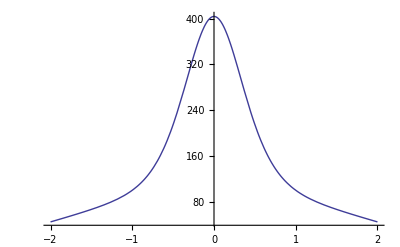

```mathematica
Plot[ Re[E^((1+s I)(1))f3[1+s I]],{s,-2,2 }]
```

```mathematica
Solve[7/(6 s^6)+67/(10 s^5)+611/(24 s^4)+331/(8 s^3)+16289/(360 s^2)+428/(15 s)==0,s]
```

{{s→Root[420+2412 #1+9165 #1^2+14895 #1^3+16289 #1^4+10272 #1^5&,1]},{s→Root[420+2412 #1+9165 #1^2+14895 #1^3+16289 #1^4+10272 #1^5&,2]},{s→Root[420+2412 #1+9165 #1^2+14895 #1^3+16289 #1^4+10272 #1^5&,3]},{s→Root[420+2412 #1+9165 #1^2+14895 #1^3+16289 #1^4+10272 #1^5&,4]},{s→Root[420+2412 #1+9165 #1^2+14895 #1^3+16289 #1^4+10272 #1^5&,5]}}

```mathematica
Residue[ 7/(6 s^6)+67/(10 s^5)+611/(24 s^4)+331/(8 s^3)+16289/(360 s^2)+428/(15 s), {s,0}]
```

428/15

```mathematica
K[n_]:=If[n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
P[n_, k_]:=Sum[ K[j] P[Floor[n/j],k-1],{j,2,n}];P[n_,0]:=1
```

```mathematica
Sum[ P[100,k]/k/s^(k),{k,1,Log[2,100]}]
```

7/(6 s^6)+67/(10 s^5)+611/(24 s^4)+331/(8 s^3)+16289/(360 s^2)+428/(15 s)

```mathematica
N[Solve[7/(6 s^6)+67/(10 s^5)+611/(24 s^4)+331/(8 s^3)+16289/(360 s^2)+428/(15 s)==0,s]]
```

{{s→-0.80859},{s→-0.228604-0.733022 ⅈ},{s→-0.228604+0.733022 ⅈ},{s→-0.159985-0.245301 ⅈ},{s→-0.159985+0.245301 ⅈ}}

```mathematica
fa[s_] :=7/(6 s^6)+67/(10 s^5)+611/(24 s^4)+331/(8 s^3)+16289/(360 s^2)+428/(15 s)
```

```mathematica
Expand[Integrate[ FullSimplify[E^(-s t)((DD[bb=200,t]-1)/t)],{t,0,Infinity}]]
Sum[ P[bb,k]/k/s^(k),{k,1,Log[2,bb]}]
```

ConditionalExpression[8/(7 s^7)+23/(3 s^6)+553/(15 s^5)+901/(12 s^4)+18523/(180 s^3)+3709/(45 s^2)+5356/(105 s),Re[s]>0]

8/(7 s^7)+23/(3 s^6)+553/(15 s^5)+901/(12 s^4)+18523/(180 s^3)+3709/(45 s^2)+5356/(105 s)

```mathematica
Expand[Integrate[ FullSimplify[E^(-s t)((DD[bb=100,t]-1))],{t,0,Infinity}]]
Sum[ P[bb,k]/s^(k+1),{k,1,Log[2,bb]}]
```

ConditionalExpression[7/s^7+67/(2 s^6)+611/(6 s^5)+993/(8 s^4)+16289/(180 s^3)+428/(15 s^2),Re[s]>0]

7/s^7+67/(2 s^6)+611/(6 s^5)+993/(8 s^4)+16289/(180 s^3)+428/(15 s^2)

```mathematica
f5[s_] := 7/s^7+67/(2 s^6)+611/(6 s^5)+993/(8 s^4)+16289/(180 s^3)+428/(15 s^2)
f6[ t_,g_ ] := 1/(2 Pi I ) Limit[ Integrate[E^(s t)f5[s],{s,g- I T, g+ I T}],T->Infinity]
```

```mathematica
f6[1,1]
```

99

```mathematica
f6[2,1]
```

481

```mathematica
f6[3,1]
```

1470

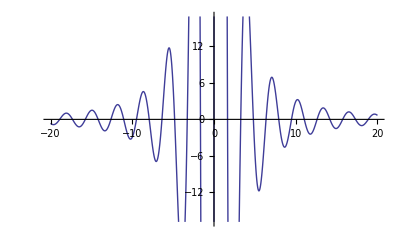

```mathematica
Plot[ Re[E^((1+s I) 2)f5[1+s I]/2Pi I],{s,-20,  20 }]
```

```mathematica
Solve[7/s^7+67/(2 s^6)+611/(6 s^5)+993/(8 s^4)+16289/(180 s^3)+428/(15 s^2)==0,s]
```

{{s→Root[2520+12060 #1+36660 #1^2+44685 #1^3+32578 #1^4+10272 #1^5&,1]},{s→Root[2520+12060 #1+36660 #1^2+44685 #1^3+32578 #1^4+10272 #1^5&,2]},{s→Root[2520+12060 #1+36660 #1^2+44685 #1^3+32578 #1^4+10272 #1^5&,3]},{s→Root[2520+12060 #1+36660 #1^2+44685 #1^3+32578 #1^4+10272 #1^5&,4]},{s→Root[2520+12060 #1+36660 #1^2+44685 #1^3+32578 #1^4+10272 #1^5&,5]}}

```mathematica
Sum[ P[bb=10,k]/s^(k+1),{k,1,Log[2,bb]}]
```

1/s^4+7/s^3+16/(3 s^2)

```mathematica
Solve[1/s^4+7/s^3+16/(3 s^2)==0,s]
```

{{s→1/32 (-21-√249)},{s→1/32 (-21+√249)}}

```mathematica
Expand[(s-1/32 (-21-√249))(s-1/32 (-21+√249))]
```

3/16+(21 s)/16+s^2

```mathematica
3/16+(21 s)/16+s^2
```

3/16+(21 s)/16+s^2

```mathematica
Sum[ x^k/k! P[bb=100,k],{k,0,Log[2,bb]}]
```

1+(428 x)/15+(16289 x^2)/360+(331 x^3)/16+(611 x^4)/144+(67 x^5)/240+(7 x^6)/720

```mathematica
fo[x_] := 1+(428 x)/15+(16289 x^2)/360+(331 x^3)/16+(611 x^4)/144+(67 x^5)/240+(7 x^6)/720
```

```mathematica
Expand[Integrate[ FullSimplify[E^(-s t)((DD[bb=100,(t+1)]-1)/(t+1))],{t,0,Infinity}]]
```

ConditionalExpression[7/(6 s^6)+118/(15 s^5)+3929/(120 s^4)+3167/(45 s^3)+6031/(60 s^2)+99/s,Re[s]>0]

```mathematica
h1[s_] := 7/(6 s^6)+118/(15 s^5)+3929/(120 s^4)+3167/(45 s^3)+6031/(60 s^2)+99/s
```

```mathematica
h2[ t_,g_ ] := 1/(2 Pi I ) Limit[ Integrate[E^(s t)h1[s],{s,g- I T, g+ I T}],T->Infinity]
```

```mathematica
h2[1,1]
```

481/2

```mathematica
h2[-1,1]
```

-428/15

```mathematica
h2[-1,100]
```

-428/15

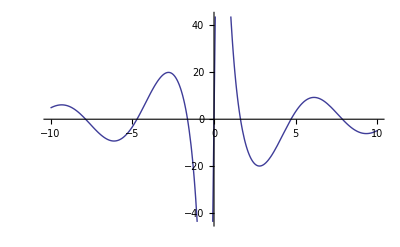

```mathematica
Plot[ Re[E^((1+s I) (-1))h1[1+s I]/2Pi I],{s,-10,  10 }]
```

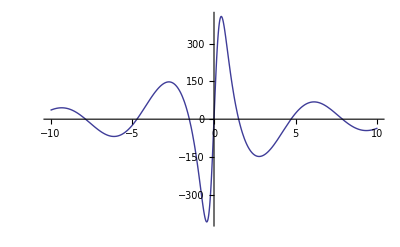

```mathematica
Plot[ Re[E^((1+s I) (1))h1[1+s I]/2Pi I],{s,-10, 10 }]
```

```mathematica
Expand[Integrate[ FullSimplify[E^(-s t)((DD[100,(t+1)]-1)/(t+1))],{t,0,Infinity}]]
```

ConditionalExpression[7/(6 s^6)+118/(15 s^5)+3929/(120 s^4)+3167/(45 s^3)+6031/(60 s^2)+99/s,Re[s]>0]

```mathematica
hx[ t_,g_ ] := 1/(2 Pi I ) Limit[ Integrate[E^(s t)Integrate[FullSimplify[E^(-s t)((DD[100,(t+1)]-1)/(t+1))],{t,0,Infinity}],{s,g- I T, g+ I T}],T->Infinity]
```

```mathematica
Integrate[FullSimplify[E^(-s t)((DDa[n,(t+1)]-1)/(t+1))],{t,0,Infinity}]
```

ConditionalExpression[(840+2 s (2832+s (11787+2 s (12668+3 s (6031+5940 s)))))/(720 s^6),Re[s]>0]

Integrate::ilim: Invalid integration variable or limit(s) in {1, 0, ∞}.

```mathematica
h1[s_] := 7/(6 s^6)+118/(15 s^5)+3929/(120 s^4)+3167/(45 s^3)+6031/(60 s^2)+99/s
Plot3D[Re[ h1[ x+I y]],{x,-.5,.5},{y,-.5,.5}]
```

```mathematica
(D2[100,2]-1)/2
```

16980

```mathematica
Expand[Integrate[ FullSimplify[E^(-s t)((DD[bb=20,(t+1)]-1)/(t+1))],{t,0,Infinity}]]
```

ConditionalExpression[1/(4 s^4)+49/(12 s^3)+137/(12 s^2)+19/s,Re[s]>0]

```mathematica
Expand[FullSimplify[E^(-s t)((DD[bb=20,(t+1)]-1)/(t+1))]]
```

19 ⅇ^(-s t)+137/12 ⅇ^(-s t) t+49/24 ⅇ^(-s t) t^2+1/24 ⅇ^(-s t) t^3

```mathematica
Expand[FullSimplify[E^(-s t)((DDo[bb=20,(t+1),1]-1)/(t+1))]]
```

(18 ⅇ^(-s t))/(1+t)+(19 ⅇ^(-s t) t)/(1+t)

```mathematica
Expand[FullSimplify[E^(-s t)((DDo[bb=20,(t+1),2]-1)/(t+1))]]
```

-ⅇ^(-s t)/(1+t)+(27 ⅇ^(-s t) t)/(2 (1+t))+(27 ⅇ^(-s t) t^2)/(2 (1+t))

```mathematica
Expand[FullSimplify[E^(-s t)((DDo[bb=20,(t+1),3]-1)/(t+1))]]
```

-ⅇ^(-s t)/(1+t)+(13 ⅇ^(-s t) FactorialPower[1+t,3])/(6 (1+t))

```mathematica
Expand[FullSimplify[E^(-s t)((DDo[bb=20,(t+1),4]-1)/(t+1))]]
```

-ⅇ^(-s t)/(1+t)+(ⅇ^(-s t) FactorialPower[1+t,4])/(24 (1+t))

```mathematica
Sum[Expand[FullSimplify[E^(-s t)((DDo[bb=20,(t+1),k]-1)/(t+1))]],{k,0,11}]
```

(8 ⅇ^(-s t))/(1+t)+(65 ⅇ^(-s t) t)/(2 (1+t))+(27 ⅇ^(-s t) t^2)/(2 (1+t))+(13 ⅇ^(-s t) FactorialPower[1+t,3])/(6 (1+t))+(ⅇ^(-s t) FactorialPower[1+t,4])/(24 (1+t))

```mathematica
19/1 + 27/2
```

65/2

```mathematica
E^(-s t)((DD[bb=20,(t+1)]-1)/(t+1))
```

1/(1+t)ⅇ^(-s t) (19 (1+t)+27/2 FactorialPower[1+t,2]+13/6 FactorialPower[1+t,3]+1/24 FactorialPower[1+t,4])

```mathematica
FactorialPower[6,2]
```

30

```mathematica
Expand[FullSimplify[E^(-s t)((DD[bb=20,(t+1)]-1)/(t+1))]]
```

19 ⅇ^(-s t)+137/12 ⅇ^(-s t) t+49/24 ⅇ^(-s t) t^2+1/24 ⅇ^(-s t) t^3

```mathematica
E^(-s t)((DDc[bb=20,(t+1)]-1)/(t+1))
```

1/(1+t)ⅇ^(-s t) (-1+D2c[20,0]+(1+t) D2c[20,1]+1/2 D2c[20,2] FactorialPower[1+t,2]+1/6 D2c[20,3] FactorialPower[1+t,3]+1/24 D2c[20,4] FactorialPower[1+t,4])

```mathematica
1/(1+t)ⅇ^(-s t) (-1+D2c[20,0]+(1+t) D2c[20,1]+1/2 D2c[20,2] (t+1)(t)+1/6 D2c[20,3] (t+1)(t)(t-1)+1/24 D2c[20,4] (t+1)(t)(t-1)(t-2))
```

```mathematica
FullSimplify[1/(1+t)ⅇ^(-s t) (-1+D2c[20,0]+(1+t) D2c[20,1]+1/2 t (1+t) D2c[20,2]+1/6 (-1+t) t (1+t) D2c[20,3]+1/24 (-2+t) (-1+t) t (1+t) D2c[20,4])]
```

1/(24 (1+t))ⅇ^(-s t) (4 (-6+6 D2c[20,0]+3 (1+t) (2 D2c[20,1]+t D2c[20,2])+t (-1+t^2) D2c[20,3])+(-2+t) (-1+t) t (1+t) D2c[20,4])

```mathematica
1/(1+t)ⅇ^(-s t) (-1+D2[20,0]+(1+t) D2[20,1]+1/2 D2[20,2] (t+1)(t)+1/6 D2[20,3] (t+1)(t)(t-1)+1/24 D2[20,4] (t+1)(t)(t-1)(t-2))
```

(ⅇ^(-s t) (19 (1+t)+27/2 t (1+t)+13/6 (-1+t) t (1+t)+1/24 (-2+t) (-1+t) t (1+t)))/(1+t)

```mathematica
FullSimplify[(ⅇ^(-s t) (19 (1+t)+27/2 t (1+t)+13/6 (-1+t) t (1+t)+1/24 (-2+t) (-1+t) t (1+t)))/(1+t)]
```

```mathematica
Expand[1/24 ⅇ^(-s t) (456+t (274+t (49+t)))]
```

19 ⅇ^(-s t)+137/12 ⅇ^(-s t) t+49/24 ⅇ^(-s t) t^2+1/24 ⅇ^(-s t) t^3

```mathematica
Expand[FullSimplify[E^(-s t)((DD[bb=20,(t+1)]-1)/(t+1))]]
```

19 ⅇ^(-s t)+137/12 ⅇ^(-s t) t+49/24 ⅇ^(-s t) t^2+1/24 ⅇ^(-s t) t^3

```mathematica
Expand[t(t-1)(t-2)(t-3)]
```

-6 t+11 t^2-6 t^3+t^4